## Fitting sigma dan eden

### Memisahkan data Pr vs ED dlm 1 file tersendiri

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP0.E+00.dat"}],{Number,Number,Number,Number,Number,Number}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"efpc_gup0E0.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[3]]}]]
```

D:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-03-03Cek\file_alka_cek_2022-03-16\fitting\efpc_gup0E0.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP1.E-07.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"efpc_gup1E-7.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[3]]}]]
```

D:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-03-03Cek\file_alka_cek_2022-03-16\fitting\efpc_gup1E-7.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP1.E-08.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"efpc_gup1E-8.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[3]]}]]
```

D:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-03-03Cek\file_alka_cek_2022-03-16\fitting\efpc_gup1E-8.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP1.E-09.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"efpc_gup1E-9.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[3]]}]]
```

D:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-03-03Cek\file_alka_cek_2022-03-16\fitting\efpc_gup1E-9.dat

### Memisahkan data σ (= Pr-Pt) vs ED dlm 1 file tersendiri

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP0.E+00.dat"}],{Number,Number,Number,Number,Number,Number}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"sfpc_gup0E0.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[5]]-Transpose[data][[6]]}]]
```

D:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-03-03Cek\file_alka_cek_2022-03-16\fitting\sfpc_gup0E0.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP1.E-07.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-7.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[5]]-Transpose[data][[6]]}]]
```

D:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-03-03Cek\file_alka_cek_2022-03-16\fitting\sfpc_gup1E-7.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP1.E-08.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-8.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[5]]-Transpose[data][[6]]}]]
```

D:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-03-03Cek\file_alka_cek_2022-03-16\fitting\sfpc_gup1E-8.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP1.E-09.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-9.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[5]]-Transpose[data][[6]]}]]
```

D:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-03-03Cek\file_alka_cek_2022-03-16\fitting\sfpc_gup1E-9.dat

### fitting anisotropik

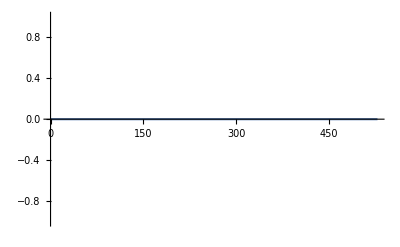

0.

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"sfpc_gup0E0.dat"}],{Number,Number}];
fitted=Fit[data,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
FortranForm[fitted]
Plot[fitted,{P0,Min[Transpose[data][[1]]],Max[Transpose[data][[1]]]}(*,Epilog->{PointSize[0.02],Map[Point,data]}*),PlotRange->Full]
```

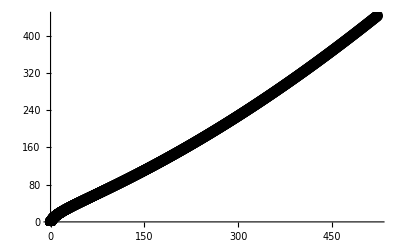

2.592491577549439 + 1.0881959659546299*P0 - 0.0067339371915666486*P0**2 + 0.00004499403194098332*P0**3 - 1.403890968893791e-7*P0**4 + 
     -  2.1380720354225518e-10*P0**5 - 1.2645243593667345e-13*P0**6

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-7.dat"}],{Number,Number}];
fitted=Fit[data,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
FortranForm[fitted]
Plot[fitted,{P0,Min[Transpose[data][[1]]],Max[Transpose[data][[1]]]},Epilog->{PointSize[0.02],Map[Point,data]}]
```

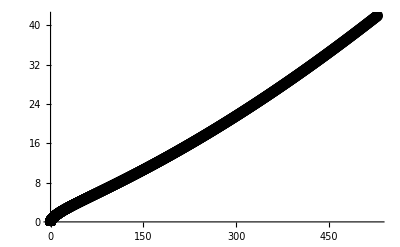

0.30701904439652133 + 0.1039495092018227*P0 - 0.0006365506206222362*P0**2 + 4.201612276546197e-6*P0**3 - 1.3005673361001568e-8*P0**4 + 
     -  1.9634090417231533e-11*P0**5 - 1.1507021099563144e-14*P0**6

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-8.dat"}],{Number,Number}];
fitted=Fit[data,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
FortranForm[fitted]
Plot[fitted,{P0,Min[Transpose[data][[1]]],Max[Transpose[data][[1]]]},Epilog->{PointSize[0.02],Map[Point,data]}]
```

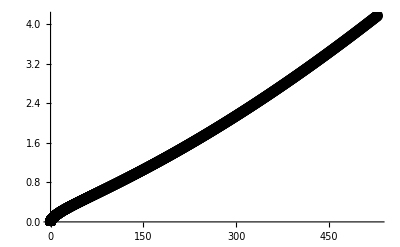

0.031145146316513446 + 0.010349211360099742*P0 - 0.00006332850044107077*P0**2 + 4.175962495200208e-7*P0**3 - 1.291925222965174e-9*P0**4 + 
     -  1.9491805101749963e-12*P0**5 - 1.1416404376861113e-15*P0**6

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-9.dat"}],{Number,Number}];
fitted=Fit[data,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
FortranForm[fitted]
Plot[fitted,{P0,Min[Transpose[data][[1]]],Max[Transpose[data][[1]]]},Epilog->{PointSize[0.02],Map[Point,data]}]
```

### fitting energy density GUP 0E0

#### Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3Crust.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCrust=data[[1;;LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]]];
```

```mathematica
dataInnerCrust=data[[LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&];;LengthWhile[Transpose[data][[1]],#<.5658&](*Dimensions[data][[1]]*)]];
```

#### GUP 0E0 + Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_gup0E0.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCore=data[[LengthWhile[Transpose[data][[1]],#<0.5658&]+1;;LengthWhile[Transpose[data][[1]],#<50.&]]];
```

```mathematica
dataInnerCore=data[[LengthWhile[Transpose[data][[1]],#<50.&]+1;;Dimensions[data][[1]]]];
```

```mathematica
tambah1={dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-4]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-3]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-2]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-1]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-0]]};
```

```mathematica
tambah2={dataOuterCore[[1]],dataOuterCore[[2]]};
```

```mathematica
dataOuterCoreNew=Join[tambah1,dataOuterCore];
```

```mathematica
dataInnerCrustNew=Join[dataInnerCrust,tambah2];
```

#### fitting

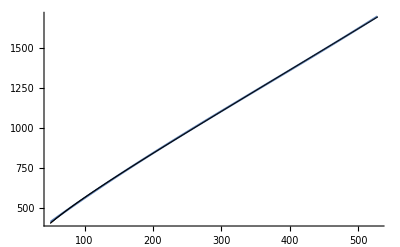

254.572+3.27227 P0-0.00199025 P0^2+1.84396×10^-6 P0^3

```mathematica
fitted=Fit[dataInnerCore,{1,P0,P0^2,P0^3},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCore][[1]]],Max[Transpose[dataInnerCore][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCore]}]
fitInnerCoreGUP0E0=fitted
```

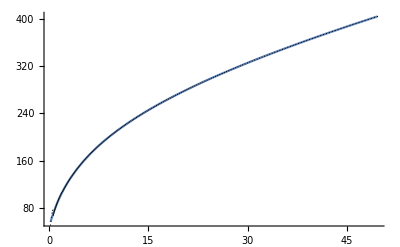

```mathematica
fitted=Fit[dataOuterCoreNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6,P0^7,P0^8,P0^9,P0^10,P0^11,P0^12,P0^13,P0^14,P0^15,P0^16,P0^17},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCoreNew][[1]]],Max[Transpose[dataOuterCoreNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCoreNew]}]
fitOuterCoreGUP0E0=fitted;
```

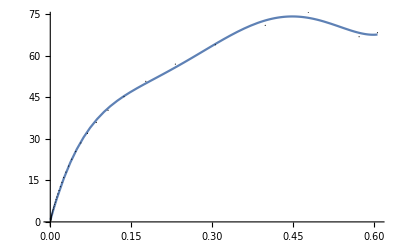

0.426006+714.24 P0-4571.21 P0^2+16153.3 P0^3-26410.3 P0^4+15662.1 P0^5

```mathematica
fitted=Fit[dataInnerCrustNew,{1,P0,P0^2,P0^3,P0^4,P0^5},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCrustNew][[1]]],Max[Transpose[dataInnerCrustNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCrustNew]}]
fitInnerCrustGUP0E0=fitted
```

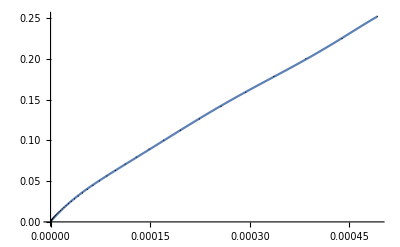

0.000233609+963.968 P0-6.02229×10^6 P0^2+3.89592×10^10 P0^3-1.29911×10^14 P0^4+2.09771×10^17 P0^5-1.29719×10^20 P0^6

```mathematica
fitted=Fit[dataOuterCrust,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCrust][[1]]],Max[Transpose[dataOuterCrust][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCrust]}]
fitOuterCrustGUP0E0=fitted
```

#### Cek hasilnya

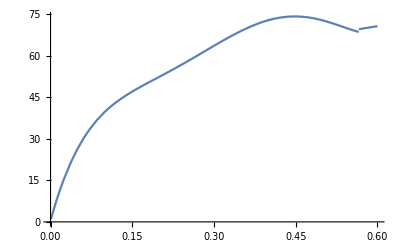

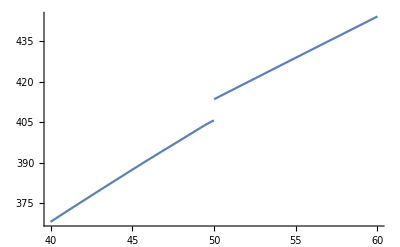

```mathematica
(* Model Neutron Star *)
FED1[P0_]=fitInnerCoreGUP0E0;
FED2[P0_]=fitOuterCoreGUP0E0;
FED3[P0_]=fitInnerCrustGUP0E0;
FED4[P0_]=fitOuterCrustGUP0E0;
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]]; (* Model Neutron Star *)
dpdϵ=1/D[ϵ[p],p];
Plot[ϵ[p],{p,0,.6}]
Plot[ϵ[p],{p,40,60},PlotRange->All]
```

#### Untuk ditulis di Fortran

```mathematica
fitInnerCoreGUP0E0//FortranForm
```

254.57247440600295 + 3.2722668135019934*P0 - 0.001990248070884927*P0**2 + 1.84396271672383e-6*P0**3

```mathematica
fitOuterCoreGUP0E0//FortranForm
```

49.26742463817125 + 39.119351704835466*P0 - 6.01896166404222*P0**2 + 0.3433694307027147*P0**3 + 0.18883140341510926*P0**4 - 
     -  0.06644121914946151*P0**5 + 0.011485498494705426*P0**6 - 0.001286305935262887*P0**7 + 0.00010130171176109097*P0**8 - 
     -  5.822797038254955e-6*P0**9 + 2.4876626925287405e-7*P0**10 - 7.949921889091221e-9*P0**11 + 1.8935665032830884e-10*P0**12 - 
     -  3.313041521451298e-12*P0**13 + 4.133738349743126e-14*P0**14 - 3.4808925256755404e-16*P0**15 + 1.772585629917586e-18*P0**16 - 
     -  4.1225826164355645e-21*P0**17

```mathematica
fitInnerCrustGUP0E0//FortranForm
```

0.426006479563915 + 714.2395621878952*P0 - 4571.210848278986*P0**2 + 16153.315408751043*P0**3 - 26410.273422295842*P0**4 + 15662.08708827184*P0**5

```mathematica
fitOuterCrustGUP0E0//FortranForm
```

0.00023360915782324394 + 963.9682663375585*P0 - 6.022287440793419e6*P0**2 + 3.895919986209412e10*P0**3 - 1.2991084452361116e14*P0**4 + 
     -  2.097713931761687e17*P0**5 - 1.2971859528646892e20*P0**6

### fitting energy density GUP 1Em7

#### Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3Crust.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCrust=data[[1;;LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]]];
```

```mathematica
dataInnerCrust=data[[LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&];;LengthWhile[Transpose[data][[1]],#<.5658&](*Dimensions[data][[1]]*)]];
```

#### GUP 1Em7 + Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_gup1E-7.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCore=data[[LengthWhile[Transpose[data][[1]],#<0.5658&]+1;;LengthWhile[Transpose[data][[1]],#<50.&]]];
```

```mathematica
dataInnerCore=data[[LengthWhile[Transpose[data][[1]],#<50.&]+1;;Dimensions[data][[1]]]];
```

```mathematica
tambah1={dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-4]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-3]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-2]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-1]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-0]]};
```

```mathematica
tambah2={(*dataOuterCore[[1]],dataOuterCore[[2]]*)};
```

```mathematica
dataOuterCoreNew=Join[tambah1,dataOuterCore];
```

```mathematica
dataInnerCrustNew=Join[dataInnerCrust,tambah2];
```

#### fitting

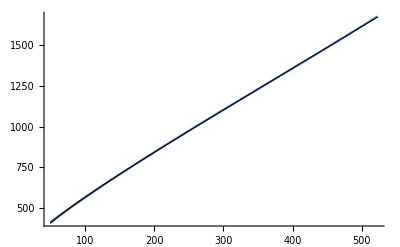

253.632+3.27521 P0-0.00204754 P0^2+1.90427×10^-6 P0^3

```mathematica
fitted=Fit[dataInnerCore,{1,P0,P0^2,P0^3},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCore][[1]]],Max[Transpose[dataInnerCore][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCore]}]
fitInnerCoreGUP1Em7=fitted
```

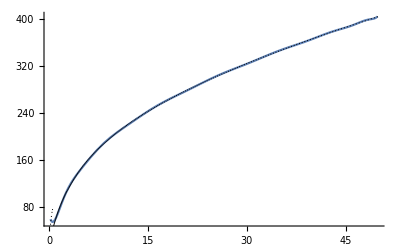

```mathematica
fitted=Fit[dataOuterCoreNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6,P0^7,P0^8,P0^9,P0^10,P0^11,P0^12,P0^13,P0^14,P0^15,P0^16},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCoreNew][[1]]],Max[Transpose[dataOuterCoreNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCoreNew]}]
fitOuterCoreGUP1Em7=fitted;
```

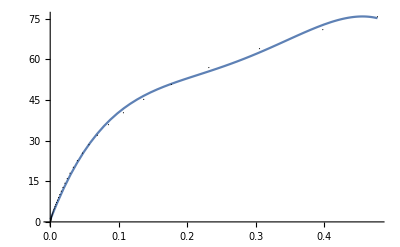

0.659656+658.782 P0-3385.41 P0^2+8513.26 P0^3-7598.18 P0^4

```mathematica
fitted=Fit[dataInnerCrustNew,{1,P0,P0^2,P0^3,P0^4(*,P0^5,P0^6,P0^7*)},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCrustNew][[1]]],Max[Transpose[dataInnerCrustNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCrustNew]}]
fitInnerCrustGUP1Em7=fitted
```

```mathematica
fitted=Fit[dataOuterCrust,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCrust][[1]]],Max[Transpose[dataOuterCrust][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCrust]}]
fitOuterCrustGUP1Em7=fitted
```

-Graphics-

0.000233609+963.968 P0-6.02229×10^6 P0^2+3.89592×10^10 P0^3-1.29911×10^14 P0^4+2.09771×10^17 P0^5-1.29719×10^20 P0^6

#### Cek hasilnya

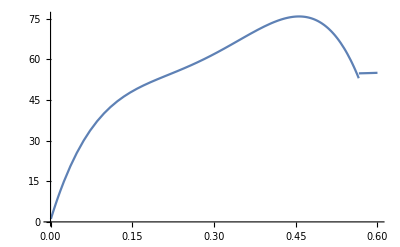

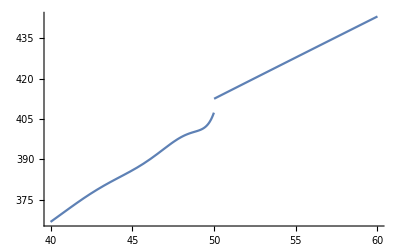

```mathematica
(* Model Neutron Star *)
FED1[P0_]=fitInnerCoreGUP1Em7;
FED2[P0_]=fitOuterCoreGUP1Em7;
FED3[P0_]=fitInnerCrustGUP1Em7;
FED4[P0_]=fitOuterCrustGUP1Em7;
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]]; (* Model Neutron Star *)
dpdϵ=1/D[ϵ[p],p];
Plot[ϵ[p],{p,0,.6}]
Plot[ϵ[p],{p,40,60},PlotRange->All]
```

#### Untuk ditulis di Fortran

```mathematica
fitInnerCoreGUP1Em7//FortranForm
```

253.63165216038928 + 3.2752062368565293*P0 - 0.0020475370384748772*P0**2 + 1.9042736185326342e-6*P0**3

```mathematica
fitOuterCoreGUP1Em7//FortranForm
```

66.96708993631238 - 56.51471366592033*P0 + 80.53251468579876*P0**2 - 38.23693260439177*P0**3 + 10.427996251960504*P0**4 - 
     -  1.8375871943706583*P0**5 + 0.22236347635004453*P0**6 - 0.019184979268615673*P0**7 + 0.001208418519118079*P0**8 - 0.00005632565076844584*P0**9 + 
     -  1.952250313381669e-6*P0**10 - 5.012092090517967e-8*P0**11 + 9.3958563916334e-10*P0**12 - 1.2491366788090967e-11*P0**13 + 
     -  1.1150846246189833e-13*P0**14 - 5.992007702614946e-16*P0**15 + 1.4644428659331378e-18*P0**16

```mathematica
fitInnerCrustGUP1Em7//FortranForm
```

0.6596556980482822 + 658.7820465828232*P0 - 3385.41205749569*P0**2 + 8513.260609472412*P0**3 - 7598.179318111874*P0**4

```mathematica
fitOuterCrustGUP1Em7//FortranForm
```

0.00023360915782324394 + 963.9682663375585*P0 - 6.022287440793419e6*P0**2 + 3.895919986209412e10*P0**3 - 1.2991084452361116e14*P0**4 + 
     -  2.097713931761687e17*P0**5 - 1.2971859528646892e20*P0**6

### fitting energy density GUP 1Em8

#### Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3Crust.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCrust=data[[1;;LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]]];
```

```mathematica
dataInnerCrust=data[[LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&];;LengthWhile[Transpose[data][[1]],#<.5658&](*Dimensions[data][[1]]*)]];
```

#### GUP 1Em8 + Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_gup1E-8.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCore=data[[LengthWhile[Transpose[data][[1]],#<0.5658&]+1;;LengthWhile[Transpose[data][[1]],#<50.&]]];
```

```mathematica
dataInnerCore=data[[LengthWhile[Transpose[data][[1]],#<50.&]+1;;Dimensions[data][[1]]]];
```

```mathematica
tambah1={dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-4]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-3]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-2]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-1]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-0]]};
```

```mathematica
tambah2={(*dataOuterCore[[1]],dataOuterCore[[2]]*)};
```

```mathematica
dataOuterCoreNew=Join[tambah1,dataOuterCore];
```

```mathematica
dataInnerCrustNew=Join[dataInnerCrust,tambah2];
```

#### fitting

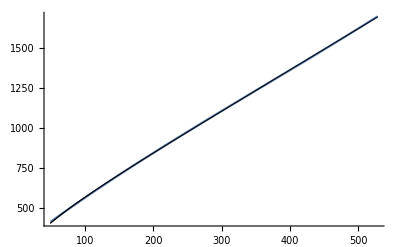

254.433+3.27305 P0-0.00199721 P0^2+1.8511×10^-6 P0^3

```mathematica
fitted=Fit[dataInnerCore,{1,P0,P0^2,P0^3},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCore][[1]]],Max[Transpose[dataInnerCore][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCore]}]
fitInnerCoreGUP1Em8=fitted
```

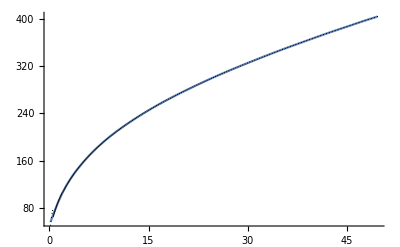

```mathematica
fitted=Fit[dataOuterCoreNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6,P0^7,P0^8,P0^9,P0^10,P0^11,P0^12,P0^13,P0^14,P0^15,P0^16},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCoreNew][[1]]],Max[Transpose[dataOuterCoreNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCoreNew]}]
fitOuterCoreGUP1Em8=fitted;
```

```mathematica
fitted=Fit[dataInnerCrustNew,{1,P0,P0^2,P0^3,P0^4(*,P0^5,P0^6,P0^7*)},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCrustNew][[1]]],Max[Transpose[dataInnerCrustNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCrustNew]}]
fitInnerCrustGUP1Em8=fitted
```

-Graphics-

0.659656+658.782 P0-3385.41 P0^2+8513.26 P0^3-7598.18 P0^4

```mathematica
fitted=Fit[dataOuterCrust,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCrust][[1]]],Max[Transpose[dataOuterCrust][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCrust]}]
fitOuterCrustGUP1Em8=fitted
```

-Graphics-

0.000233609+963.968 P0-6.02229×10^6 P0^2+3.89592×10^10 P0^3-1.29911×10^14 P0^4+2.09771×10^17 P0^5-1.29719×10^20 P0^6

#### Cek hasilnya

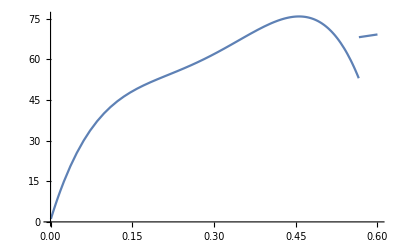

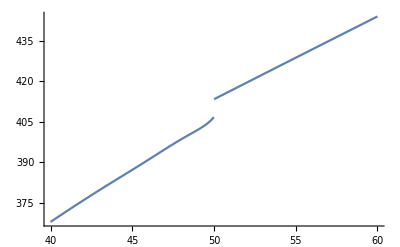

```mathematica
(* Model Neutron Star *)
FED1[P0_]=fitInnerCoreGUP1Em8;
FED2[P0_]=fitOuterCoreGUP1Em8;
FED3[P0_]=fitInnerCrustGUP1Em8;
FED4[P0_]=fitOuterCrustGUP1Em8;
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]]; (* Model Neutron Star *)
dpdϵ=1/D[ϵ[p],p];
Plot[ϵ[p],{p,0,.6}]
Plot[ϵ[p],{p,40,60},PlotRange->All]
```

#### Untuk ditulis di Fortran

```mathematica
fitInnerCoreGUP1Em8//FortranForm
```

254.43269461971036 + 3.273054555571257*P0 - 0.001997209235201446*P0**2 + 1.851100232857492e-6*P0**3

```mathematica
fitOuterCoreGUP1Em8//FortranForm
```

51.10110347547388 + 29.580362175576692*P0 + 2.536105893721721*P0**2 - 3.362838524003126*P0**3 + 1.126555289123373*P0**4 - 
     -  0.21779067821540893*P0**5 + 0.027827154930995395*P0**6 - 0.00249040782957623*P0**7 + 0.00016113586173675392*P0**8 - 7.669343460675428e-6*P0**9 + 
     -  2.7037514338561945e-7*P0**10 - 7.041371129203956e-9*P0**11 + 1.3364102402868038e-10*P0**12 - 1.796203085029556e-12*P0**13 + 
     -  1.6192812130330923e-14*P0**14 - 8.779890162813716e-17*P0**15 + 2.1637251708971996e-19*P0**16

```mathematica
fitInnerCrustGUP1Em8//FortranForm
```

0.6596556980482822 + 658.7820465828232*P0 - 3385.41205749569*P0**2 + 8513.260609472412*P0**3 - 7598.179318111874*P0**4

```mathematica
fitOuterCrustGUP1Em8//FortranForm
```

0.00023360915782324394 + 963.9682663375585*P0 - 6.022287440793419e6*P0**2 + 3.895919986209412e10*P0**3 - 1.2991084452361116e14*P0**4 + 
     -  2.097713931761687e17*P0**5 - 1.2971859528646892e20*P0**6

### fitting energy density GUP 1Em9

#### Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3Crust.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCrust=data[[1;;LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]]];
```

```mathematica
dataInnerCrust=data[[LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&];;LengthWhile[Transpose[data][[1]],#<.5658&](*Dimensions[data][[1]]*)]];
```

#### GUP 1Em9 + Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_gup1E-9.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCore=data[[LengthWhile[Transpose[data][[1]],#<0.5658&]+1;;LengthWhile[Transpose[data][[1]],#<50.&]]];
```

```mathematica
dataInnerCore=data[[LengthWhile[Transpose[data][[1]],#<50.&]+1;;Dimensions[data][[1]]]];
```

```mathematica
tambah1={dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-4]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-3]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-2]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-1]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-0]]};
```

```mathematica
tambah2={(*dataOuterCore[[1]],dataOuterCore[[2]]*)};
```

```mathematica
dataOuterCoreNew=Join[tambah1,dataOuterCore];
```

```mathematica
dataInnerCrustNew=Join[dataInnerCrust,tambah2];
```

#### fitting

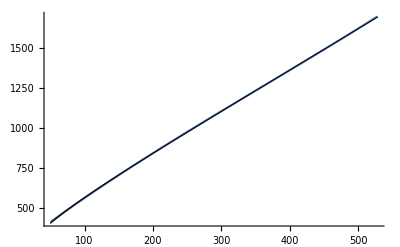

254.559+3.27234 P0-0.00199093 P0^2+1.84466×10^-6 P0^3

```mathematica
fitted=Fit[dataInnerCore,{1,P0,P0^2,P0^3},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCore][[1]]],Max[Transpose[dataInnerCore][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCore]}]
fitInnerCoreGUP1Em9=fitted
```

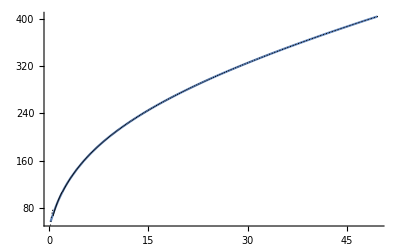

```mathematica
fitted=Fit[dataOuterCoreNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6,P0^7,P0^8,P0^9,P0^10,P0^11,P0^12,P0^13,P0^14,P0^15,P0^16},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCoreNew][[1]]],Max[Transpose[dataOuterCoreNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCoreNew]}]
fitOuterCoreGUP1Em9=fitted;
```

```mathematica
fitted=Fit[dataInnerCrustNew,{1,P0,P0^2,P0^3,P0^4(*,P0^5,P0^6,P0^7*)},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCrustNew][[1]]],Max[Transpose[dataInnerCrustNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCrustNew]}]
fitInnerCrustGUP1Em9=fitted
```

-Graphics-

0.659656+658.782 P0-3385.41 P0^2+8513.26 P0^3-7598.18 P0^4

```mathematica
fitted=Fit[dataOuterCrust,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCrust][[1]]],Max[Transpose[dataOuterCrust][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCrust]}]
fitOuterCrustGUP1Em9=fitted
```

-Graphics-

0.000233609+963.968 P0-6.02229×10^6 P0^2+3.89592×10^10 P0^3-1.29911×10^14 P0^4+2.09771×10^17 P0^5-1.29719×10^20 P0^6

#### Cek hasilnya

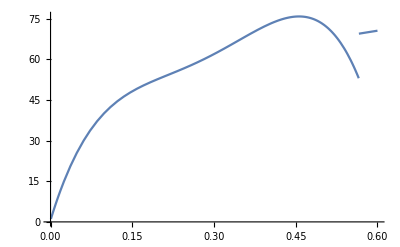

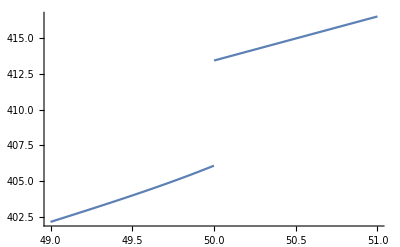

```mathematica
(* Model Neutron Star *)
FED1[P0_]=fitInnerCoreGUP1Em9;
FED2[P0_]=fitOuterCoreGUP1Em9;
FED3[P0_]=fitInnerCrustGUP1Em9;
FED4[P0_]=fitOuterCrustGUP1Em9;
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]]; (* Model Neutron Star *)
dpdϵ=1/D[ϵ[p],p];
Plot[ϵ[p],{p,0,.6}]
Plot[ϵ[p],{p,49,51},PlotRange->All]
```

#### Untuk ditulis di Fortran

```mathematica
fitInnerCoreGUP1Em9//FortranForm
```

254.55864437626303 + 3.272343184890175*P0 - 0.0019909310765835937*P0**2 + 1.8446607437157493e-6*P0**3

```mathematica
fitOuterCoreGUP1Em9//FortranForm
```

49.347044868847675 + 38.74310609538898*P0 - 6.020600747898559*P0**2 + 0.5480790714664272*P0**3 + 0.0671605654123523*P0**4 - 
     -  0.031129725932366903*P0**5 + 0.0051950965783228885*P0**6 - 0.0005322011739328282*P0**7 + 0.000037383109189199726*P0**8 - 
     -  1.8802057068517032e-6*P0**9 + 6.895336131346411e-8*P0**10 - 1.8494869902025548e-9*P0**11 + 3.590939846404496e-11*P0**12 - 
     -  4.913868612157229e-13*P0**13 + 4.494366268951504e-15*P0**14 - 2.4658392016208844e-17*P0**15 + 6.136484238830614e-20*P0**16

```mathematica
fitInnerCrustGUP1Em9//FortranForm
```

0.6596556980482822 + 658.7820465828232*P0 - 3385.41205749569*P0**2 + 8513.260609472412*P0**3 - 7598.179318111874*P0**4

```mathematica
fitOuterCrustGUP1Em9//FortranForm
```

0.00023360915782324394 + 963.9682663375585*P0 - 6.022287440793419e6*P0**2 + 3.895919986209412e10*P0**3 - 1.2991084452361116e14*P0**4 + 
     -  2.097713931761687e17*P0**5 - 1.2971859528646892e20*P0**6

## Tes

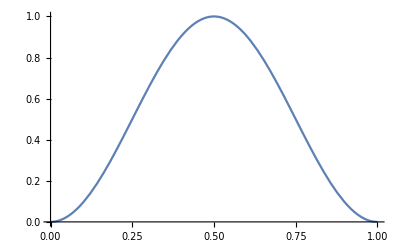

```mathematica
Plot[Sin[π x]^2,{x,0,1}]
```

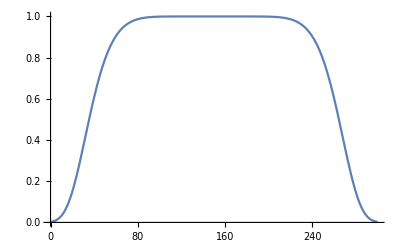

```mathematica
Plot[Exp[-(x-300/2)^8/(300/2.5)^8],{x,0,300},PlotRange->All]
```